```mathematica
ClearAll["Global`*"]
(* set your home directory *)
SetDirectory[NotebookDirectory[]];
```

# Red–Green refinement for triangular meshes

```mathematica
(* import nodes and triangles *)
nodes=Import["nOld.dat","Table"];
(* Mathematica counts from 1 not 0 *)
triangles=Import["tOld.dat","Table"]+1;
redTriangles =Import["tRed.dat","List"]+1;
elements=Triangle/@triangles; (* map Triangles[] at each element of list of triangles *)
elements=MapAt[Style[#,Red]&,elements,List/@redTriangles];
𝒦=MeshRegion[nodes,elements];
```

```mathematica
(* refined mesh *)
nodes=Import["nNew.dat","Table"];
triangles=Import["tNew.dat","Table"]+1;
Subscript[𝒦, refined]=MeshRegion[nodes,Line[triangles]];
```

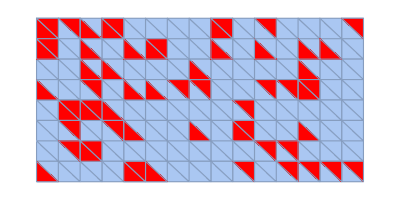

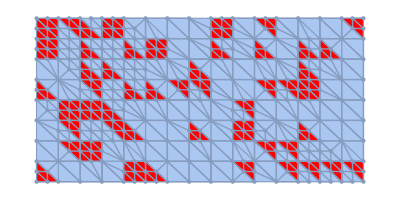

```mathematica
(* let’s plot old and refined triangulations *)
𝒦
Show[𝒦,Subscript[𝒦, refined]]
```